# Practical 2 (Secant Method)

## Ques 1. Solve x^3 - 2x - 5 = 0 Solution:

```mathematica
f[x_]:=x^3 - 2 x - 5 
Subscript[x, 0]=2;
Subscript[x, 1]=3;
e= 0.000001;
iterations=10;
If[f[Subscript[x, 0]]*f[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [ Subscript[x, n-1] - f[Subscript[x, n-1]]  * (Subscript[x, n-1]-Subscript[x, n-2])/(f[Subscript[x, n-1]]-f[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]
```

1th iteration is: 2.05882

Estimated error: 0.941176

2th iteration is: 2.08126

Estimated error: 0.0224401

3th iteration is: 2.09482

Estimated error: 0.0135605

4th iteration is: 2.09455

Estimated error: 0.000274715

5th iteration is: 2.09455

Estimated error: 2.05019×10^-6

Return[2.09455]

Approximate Root 2.09455

## Q2. Find approximate root of following equations using the secant method: i) x^3-3 x^2+2x+5=0 ii) Cos(x) - xe^x=0 iii)e^-x=x Solution: i)x^3-3 x^2+2x+5=0

1th iteration is: -0.833333

Estimated error: 0.833333

2th iteration is: -0.962567

Estimated error: 0.129234

3th iteration is: -0.901757

Estimated error: 0.0608094

4th iteration is: -0.904081

Estimated error: 0.00232406

5th iteration is: -0.904161

Estimated error: 0.0000794928

Return[-0.904161]

Approximate Root -0.904161

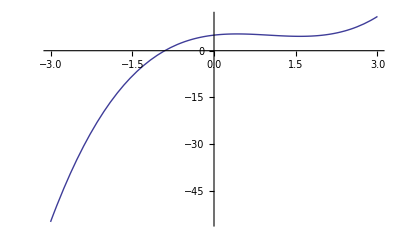

```mathematica
g[x_]:=x^3 -3  x^2+ 2 x + 5 
Subscript[x, 0]=-1;
Subscript[x, 1]=0;
e= 0.000001;
iterations=10;
If[g[Subscript[x, 0]]*g[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [ Subscript[x, n-1] - g[Subscript[x, n-1]]  * (Subscript[x, n-1]-Subscript[x, n-2])/(g[Subscript[x, n-1]]-g[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]

Plot[g[x],{x,-3,3}]
```

# ii) Cos(x) - xe^x=0

1th iteration is: 1.5649

Estimated error: 0.435096

2th iteration is: 1.57098

Estimated error: 0.00607467

3th iteration is: 1.5708

Estimated error: 0.000182263

Return[1.5708]

Approximate Root 1.5708

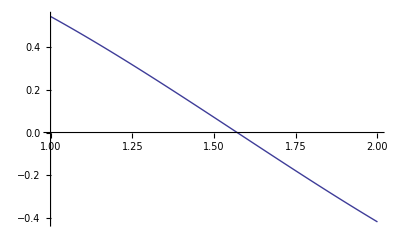

```mathematica
k[x_]:=Cos[x]-x e^(x) 
Subscript[x, 0]=1;
Subscript[x, 1]=2;
e= 0.000001;
iterations=10;
If[k[Subscript[x, 0]]*k[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [ Subscript[x, n-1] - k[Subscript[x, n-1]]  * (Subscript[x, n-1]-Subscript[x, n-2])/(k[Subscript[x, n-1]]-k[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]

Plot[k[x],{x,1,2}]
```

## iii)e^-x=x

1th iteration is: 0.6127

Estimated error: 0.3873

2th iteration is: 0.563838

Estimated error: 0.0488614

3th iteration is: 0.56717

Estimated error: 0.00333197

4th iteration is: 0.567143

Estimated error: 0.0000270518

Return[0.567143]

Approximate Root 0.567143

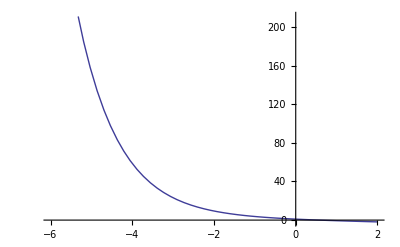

```mathematica
k[x_]:=ⅇ^-x-x
Subscript[x, 0]=0;
Subscript[x, 1]=1;
e= 0.000001;
iterations=10;
If[k[Subscript[x, 0]]*k[Subscript[x, 1]]>0,Print["These values do not satisfy the IVP so change the initial value."], 
For[n=2,n≤iterations,n++,
Subscript[x, n] = N [ Subscript[x, n-1] - k[Subscript[x, n-1]]  * (Subscript[x, n-1]-Subscript[x, n-2])/(k[Subscript[x, n-1]]-k[Subscript[x, n-2]])];
If[Abs[Subscript[x, n]-Subscript[x, n-1]]<e ,Return[Subscript[x, n]]];
Print[n-1,"th iteration is: ",Subscript[x, n]]; 
Print ["Estimated error: ",Abs[Subscript[x, n]-Subscript[x, n-1]]]]];
Print["Approximate Root ", Subscript[x, n]]

Plot[k[x],{x,-6,2}]
```